## Fitness landscape plot

## Generating data

```mathematica
Get[FileNameJoin[{NotebookDirectory[], "GeneticAlgorithmPackage.wl"}]]
```

```mathematica
ClearAll[fDistr, init3];
fDistr[x_] := N[PDF[MultinormalDistribution[{3,3},{{1,-1/3},{-1/3,2/3}}], x]];
init3 = {1, 1};
c3[x_] := True;
 
result = GeneticAlgorithm[init3, fDistr, {c3}];
result = Transpose[result];
```

## Convergence

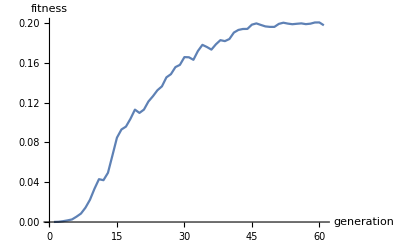

```mathematica
resultPlot = Map[
	With[
		{element = #},
		Map[
			With[
				{elementTime = #},
				fDistr[elementTime]
			]&,
			element
		]
	]&
	,
	result
];
ListLinePlot[Mean[resultPlot], AxesLabel->{generation, fitness}]
```

## Landscape

```mathematica
plot3D=Plot3D[fDistr[{x, y}], {x, 0, 5}, {y, 0, 5}, AspectRatio->Automatic, ColorFunction->"Rainbow", Mesh->None, PlotPoints->25,BoxRatios->{1, 1, 1}];
```

```mathematica
graphics=Table[Graphics3D[{Black, PointSize->Medium,
			Point[{#[[i]][[1]], #[[i]][[2]], fDistr[{#[[i]][[1]], #[[i]][[2]]}]}& /@ result]}, 
			PlotRange->{{0,5},{0,5}, Automatic}
		],
		{i, 1, Length[First[result]]}];
```

```mathematica
Manipulate[		
	Show[
		plot3D,
		graphics[[i]],
		Boxed->False, Axes->False		
	],
	{i, 1, Length[First[result]],1}
]
```

## Save GIF

```mathematica
dat = Table[Show[plot3D, graphics[[i]], Boxed->False, Axes->False],{i, 1, Length[First[result]], 1}];
SetDirectory@NotebookDirectory[]
Export["gif.gif", dat]
```

C:\Users\emtcsig\Google Drive\Research\ResearchMaterial\Wolfram\GeneticAlgorithmFramework\Framework

gif.gif

## Static plot

```mathematica
meanPoints = 
	Map[
		{#[[1]], #[[2]], fDistr[{#[[1]], #[[2]]}]}&,
		Map[
			Mean[#]&,
			Transpose[result]
		]
	];

diversity = Variance[#[[1]]&/@#]& /@ Transpose[result];

(*meanPoints = Select[meanPoints, OddQ[Position[meanPoints, #][[1]]][[1]]&];*)
meanPoints = meanPoints[[1;;-14;;2]]

lines = Tube[Map[{meanPoints[[#]], meanPoints[[#+1]]}&, Range[Length[meanPoints]-1]], 0.01];

Show[
	plot3D,
	(*Graphics3D[{PointSize->Medium, Point[meanPoints]}],*)
	Graphics3D[{Red, lines}],
	Boxed->False, Axes->False		
]

elevatedPoints = {meanPoints[[#]][[1]], meanPoints[[#]][[2]], fDistr[{meanPoints[[#]][[1]], meanPoints[[#]][[2]]}]+diversity[[#]]}& /@ Range[Length[meanPoints]];
linesUp = {meanPoints[[#]], elevatedPoints[[#]]}& /@ Range[Length[meanPoints]];

Show[
	plot3D,
	Graphics3D[{Black, PointSize->Medium, Point[elevatedPoints]}],
	Graphics3D[{Red,lines}],
	Graphics3D[{Black, Line[linesUp]}],
	Boxed->False, Axes->False, PlotRange->All	
]
```

{{1.0236,0.989715,0.0000497413},{1.09317,1.44277,0.000457515},{1.1227,1.83709,0.00205905},{1.4283,1.93807,0.00645769},{1.75973,2.05995,0.0190284},{1.88638,2.31085,0.0417534},{1.96322,2.30509,0.0470838},{2.14826,2.48941,0.084178},{2.26692,2.47616,0.0959624},{2.37065,2.51562,0.113529},{2.3342,2.54248,0.112915},{2.41993,2.57359,0.127719},{2.53301,2.55378,0.138198},{2.63919,2.56345,0.151356},{2.67586,2.61433,0.162692},{2.67406,2.66998,0.170284},{2.67118,2.76209,0.181457},{2.71697,2.72352,0.181264},{2.73067,2.75868,0.186576},{2.8028,2.76908,0.19347},{2.76467,2.86409,0.199283},{2.8066,2.95705,0.207408},{2.82361,3.00947,0.209773},{2.82096,3.04999,0.210116}}

-Graphics3D-

-Graphics3D-

## Combined plot

```mathematica
Manipulate[
	Panel[
		Panel[
			Show[
				ListLinePlot[Mean[resultPlot], AxesLabel->{"generation", "fitness"}],
				Graphics[{Red, Line[{{i, 0}, {i, 0.3}}]}]
			],
			Alignment->Center
		],
		Panel[
			Show[
				plot3D,
				graphics[[i]]	
			],
			Alignment->Center
		]
	],
	{i, 1, Length[First[result]],1}
]
```